```mathematica
(*Chemotactic response function K(t)*)
```

```mathematica
K[t_] =Piecewise[ {{1/γ ⅇ^(-t/γ) β (t/γ-t^2/(2 γ^2)),t>0},{0,t<0}}]
```

Piecewise[{{(ⅇ^(-t/γ) β (-t^2/(2 γ^2)+t/γ))/γ, t>0}, {0, True}}]

```mathematica
Integrate[γ^2*K[t],{t,0,a}, Assumptions->{γ>0,a>0}]
```

1/2 a^2 ⅇ^(-a/γ) β

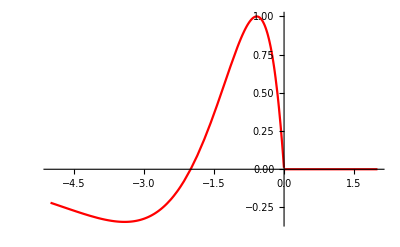

```mathematica
p1=Plot[Piecewise[{{ⅇ^t (-t-t^2/2)/((Sqrt[2]-1)*E^(Sqrt[2]-2)) ,t<0},{0,t≥0}}],{t,-5,2},PlotStyle->Red]
```

```mathematica
(*Autocorrelation function of landscape S(x)*)
```

```mathematica
R[t_,τ_] =σ^2 ⅇ^(-RealAbs[t-τ]/μ)
```

ⅇ^(-RealAbs[t-τ]/μ) σ^2

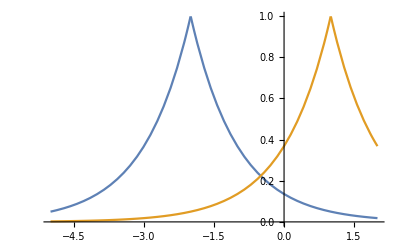

```mathematica
p2=Plot[Evaluate[Table[ ⅇ^(-RealAbs[t-τ]),{τ,{-2,1}}]],{t,-5,2}]
```

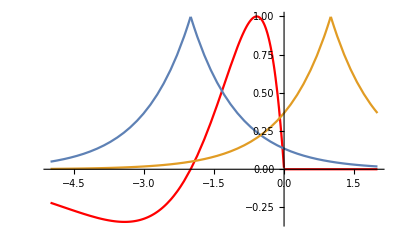

```mathematica
Show[p1,p2]
```

```mathematica
(*Input-output covariance C_\eta\Lambda(t'-v-t)*)
```

```mathematica
Subscript[C, ηλ] = Integrate[ R[u,τ]*K[u],{u,0,Infinity},Assumptions->{σ>0,β>0,γ>0,μ>0}]//FullSimplify
```

Piecewise[{{(ⅇ^(τ/μ) β γ μ^2 σ^2)/(γ+μ)^3, τ≤0}, {(ⅇ^(-(1/γ+1/μ) τ) β μ σ^2 (ⅇ^(τ/γ) γ^2 μ (γ+μ)^3-ⅇ^(τ/μ) (2 γ^2 μ^2 (3 γ^2+μ^2)+2 γ (-γ^4+μ^4) τ+(γ^2-μ^2)^2 τ^2)))/(γ (γ^2-μ^2)^3), True}}]

```mathematica
(*Check numerically*)
```

```mathematica
Subscript[C, ηλ]/.γ->2/.μ->1/.σ-> 1/.β-> 1/.τ->1//N(*Assumed parameters*)
```

0.14046

```mathematica
INTN[γ_,μ_,τ_]:=NIntegrate[1/γ*Exp[-v/γ-Abs[v-τ]/μ]*(v/γ-v^2/(2γ^2)),{v,0,Infinity}]
INTN[2,1,1]
```

0.14046

```mathematica
(*Check blow-up*)
```

```mathematica
Limit[Subscript[C, ηλ]/.γ->2/.τ->1/.σ-> 1/.β-> 1,μ->2]//N
INTN[2,2,1]
```

0.176905

0.176905

```mathematica
IOcorr[β_,σ_,μ_,γ_,τ_] = Piecewise[{{(ⅇ^(τ/μ) β γ μ^2 σ^2)/(γ+μ)^3, τ≤0}, {(ⅇ^(-(1/γ+1/μ) τ) β μ σ^2 (ⅇ^(τ/γ) γ^2 μ (γ+μ)^3-ⅇ^(τ/μ) (2 γ^2 μ^2 (3 γ^2+μ^2)+2 γ (-γ^4+μ^4) τ+(γ^2-μ^2)^2 τ^2)))/(γ (γ^2-μ^2)^3), True}}]
```

Piecewise[{{(ⅇ^(τ/μ) β γ μ^2 σ^2)/(γ+μ)^3, τ≤0}, {(ⅇ^((-1/γ-1/μ) τ) β μ σ^2 (ⅇ^(τ/γ) γ^2 μ (γ+μ)^3-ⅇ^(τ/μ) (2 γ^2 μ^2 (3 γ^2+μ^2)+2 γ (-γ^4+μ^4) τ+(γ^2-μ^2)^2 τ^2)))/(γ (γ^2-μ^2)^3), True}}]

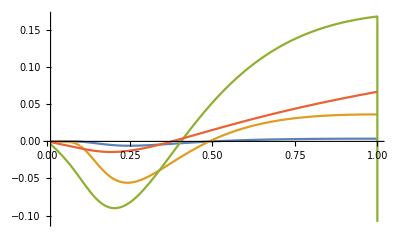

```mathematica
Plot[Evaluate[Table[ IOcorr[1,1,μ,γ,1] ,{μ,{0.01,0.1,1,10}}]],{γ,0.01,1}]
```

General::munfl: Exp[-1017.98] is too small to represent as a normalized machine number; precision may be lost.

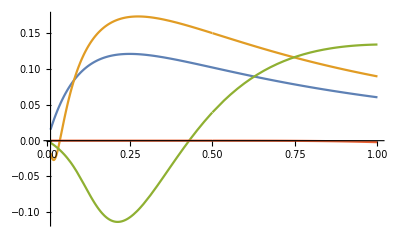

```mathematica
Plot[Evaluate[Table[ IOcorr[1,1,0.5,γ,τ ],{τ,{-0.1,0.1,1,10}}]],{γ,0.01,1}]
```

```mathematica
(*Response variance \sigma_\Lambda in Eq. (S25)*)
```

```mathematica
Subscript[σ, λ]=Integrate[Subscript[C, ηλ]*K[τ],{τ,0,Infinity},Assumptions->{γ>0,μ>0}]
```

(β^2 γ μ (γ+3 μ) σ^2)/(8 (γ+μ)^3)

```mathematica
(*deGennes derivation of the first-order KS velocity*)
```

```mathematica
INT1 = Integrate[t-u,{t,u,s}]//FullSimplify
```

1/2 (s-u)^2

```mathematica
INT2 =  Integrate[Exp[-s]INT1,{s,u,Infinity},Assumptions->{γ>0}]
```

ⅇ^-u

```mathematica
vKS[α_, β_,γ_] =α  Integrate[INT2*K[u],{u,0,Infinity},Assumptions->{γ>0}]
```

(α β γ)/(1+γ)^3

```mathematica
(*Find local maximum*)
FindMaximum[{vKS[1,1 ,γ] *27/4,0≤γ≤1},{γ,0.25}]
```

{1.,{γ→0.5}}

```mathematica
(*Integrate I-O covariance to get 2nd-order velocity correction*)
```

```mathematica
Subscript[C, ηλ]=Subscript[C, ηλ]/.τ->OverTilde[t]-v-t
```

Piecewise[{{(ⅇ^((-t-v+t̃)/μ) β γ μ^2 σ^2)/(γ+μ)^3, -t-v+t̃≤0}, {(ⅇ^(-(1/γ+1/μ) (-t-v+t̃)) β μ σ^2 (ⅇ^((-t-v+t̃)/γ) γ^2 μ (γ+μ)^3-ⅇ^((-t-v+t̃)/μ) (2 γ^2 μ^2 (3 γ^2+μ^2)+2 γ (-γ^4+μ^4) (-t-v+t̃)+(γ^2-μ^2)^2 (-t-v+t̃)^2)))/(γ (γ^2-μ^2)^3), True}}]

```mathematica
I1=Integrate[Subscript[C, ηλ], {OverTilde[t], t+v, s}, Assumptions -> {s ≥ 0, t≥0,v≥0, μ > 0,γ>0}]//FullSimplify
```

Piecewise[{{-(ⅇ^(-(t+v)/μ) (-ⅇ^(s/μ)+ⅇ^((t+v)/μ)) β γ μ^3 σ^2)/(γ+μ)^3, (((s==t&&v>0)||(v≥0&&s<t))&&(s==0||(s≥0&&t≠0)))||(s≥0&&((s>t&&s<t+v&&((t≥0&&s≤v)||t>0))||(v>0&&s≤t&&s≤v)))}, {1/((-γ^2+μ^2)^3)ⅇ^(-s/γ) β μ (4 s γ (γ-μ) μ^2 (γ+μ)-s^2 (γ^2-μ^2)^2+γ μ^2 (-2 γ^3+ⅇ^(s/γ) γ^3-3 ⅇ^(s/γ) γ^2 μ-6 γ μ^2+3 ⅇ^(s/γ) γ μ^2-ⅇ^(s/γ) μ^3+ⅇ^(s (1/γ-1/μ)) (γ+μ)^3)) σ^2, t==0&&v==0&&s>0}, {1/((γ-μ)^3 (γ+μ)^3)ⅇ^(-s (1/γ+1/μ)) β μ (-ⅇ^(s (1/γ+1/μ)) γ (γ-μ)^3 μ^2-ⅇ^(s/γ+v/μ) γ μ^2 (γ+μ)^3+ⅇ^(v/γ+s/μ) ((s-v)^2 γ^4-2 γ^2 ((s-v)^2+2 (s-v) γ-γ^2) μ^2+((s-v)^2+4 (s-v) γ+6 γ^2) μ^4)) σ^2, t==0&&v>0&&v<s}, {1/((γ-μ)^3 (γ+μ)^3)ⅇ^(-s (1/γ+1/μ)) β μ (-ⅇ^(s (1/γ+1/μ)) γ (γ-μ)^3 μ^2-ⅇ^(s/γ+(t+v)/μ) γ μ^2 (γ+μ)^3+ⅇ^((t+v)/γ+s/μ) ((-s+t+v)^2 γ^4-2 γ^2 ((-s+t+v)^2+2 (s-t-v) γ-γ^2) μ^2+((-s+t+v)^2+4 (s-t-v) γ+6 γ^2) μ^4)) σ^2, t>0&&v≥0&&t+v<s}, {0, True}}]

```mathematica
I2=Integrate[I1, {t, 0, s-v}, Assumptions -> { s ≥ 0,v≥0, μ > 0,γ>0}]//FullSimplify
```

Piecewise[{{-1/((γ-μ)^3 (γ+μ)^3)ⅇ^(-s (1/γ+1/μ)) β γ μ (-ⅇ^(s/γ+v/μ) μ^3 (γ+μ)^3-ⅇ^(s (1/γ+1/μ)) (γ-μ)^3 (2 γ^3+6 γ^2 μ+(-s+v+6 γ) μ^2+μ^3)+ⅇ^(v/γ+s/μ) (γ^4 ((s-v)^2+2 (s-v) γ+2 γ^2)-2 γ^2 (s-v+γ) (s-v+3 γ) μ^2+((s-v)^2+6 (s-v) γ+12 γ^2) μ^4)) σ^2, v≥0&&s>v}, {0, True}}]

```mathematica
I3=Integrate[I2*K[v], {v, 0, Infinity}, Assumptions -> {γ>0 , μ>0,s>0 }]
```

-1/(60 γ^2 (γ-μ)^6 (γ+μ)^3)ⅇ^(-s (1/γ+1/μ)) β^2 μ (-ⅇ^(s/μ) s^5 γ^7+3 ⅇ^(s/μ) s^5 γ^6 μ-ⅇ^(s/μ) s^5 γ^5 μ^2+10 ⅇ^(s/μ) s^4 γ^6 μ^2-20 ⅇ^(s/μ) s^3 γ^7 μ^2-30 ⅇ^(s/μ) s^2 γ^8 μ^2-60 ⅇ^(s/μ) s γ^9 μ^2+60 ⅇ^(s (1/γ+1/μ)) γ^10 μ^2-60 ⅇ^(s/μ) γ^10 μ^2-5 ⅇ^(s/μ) s^5 γ^4 μ^3-30 ⅇ^(s/μ) s^4 γ^5 μ^3+60 ⅇ^(s/μ) s^3 γ^6 μ^3+210 ⅇ^(s/μ) s^2 γ^7 μ^3+360 ⅇ^(s/μ) s γ^8 μ^3-360 ⅇ^(s (1/γ+1/μ)) γ^9 μ^3+360 ⅇ^(s/μ) γ^9 μ^3+5 ⅇ^(s/μ) s^5 γ^3 μ^4+20 ⅇ^(s/μ) s^4 γ^4 μ^4-120 ⅇ^(s/μ) s^3 γ^5 μ^4-420 ⅇ^(s/μ) s^2 γ^6 μ^4-960 ⅇ^(s/μ) s γ^7 μ^4+900 ⅇ^(s (1/γ+1/μ)) γ^8 μ^4-900 ⅇ^(s/μ) γ^8 μ^4+ⅇ^(s/μ) s^5 γ^2 μ^5+20 ⅇ^(s/μ) s^4 γ^3 μ^5+200 ⅇ^(s/μ) s^3 γ^4 μ^5+540 ⅇ^(s/μ) s^2 γ^5 μ^5+1080 ⅇ^(s/μ) s γ^6 μ^5-60 ⅇ^(s/γ) γ^7 μ^5-1200 ⅇ^(s (1/γ+1/μ)) γ^7 μ^5+1260 ⅇ^(s/μ) γ^7 μ^5-3 ⅇ^(s/μ) s^5 γ μ^6-30 ⅇ^(s/μ) s^4 γ^2 μ^6-180 ⅇ^(s/μ) s^3 γ^3 μ^6-510 ⅇ^(s/μ) s^2 γ^4 μ^6-900 ⅇ^(s/μ) s γ^5 μ^6-180 ⅇ^(s/γ) γ^6 μ^6+900 ⅇ^(s (1/γ+1/μ)) γ^6 μ^6-720 ⅇ^(s/μ) γ^6 μ^6+ⅇ^(s/μ) s^5 μ^7+10 ⅇ^(s/μ) s^4 γ μ^7+60 ⅇ^(s/μ) s^3 γ^2 μ^7+210 ⅇ^(s/μ) s^2 γ^3 μ^7+480 ⅇ^(s/μ) s γ^4 μ^7-180 ⅇ^(s/γ) γ^5 μ^7-360 ⅇ^(s (1/γ+1/μ)) γ^5 μ^7+540 ⅇ^(s/μ) γ^5 μ^7-60 ⅇ^(s/γ) γ^4 μ^8+60 ⅇ^(s (1/γ+1/μ)) γ^4 μ^8) σ^2

```mathematica
I4=Integrate[I3* Exp[-s], {s, 0, Infinity}, Assumptions -> {γ>0 , μ>0 }]
```

(β^2 γ^2 μ (2 γ^3+2 γ^2 (3+γ) μ+(-1+γ (3+γ (3+γ))) μ^2) σ^2)/((1+γ)^6 (1+μ) (γ+μ)^3)

```mathematica
(*Check limits*)
```

```mathematica
Limit[I4,μ->0]
```

0

```mathematica
Limit[I4,μ->Infinity]
```

0

```mathematica
Limit[I4,γ->Infinity]
```

0

```mathematica
Limit[I4,γ->0]
```

0

```mathematica
(*Plot*)
vcorr[β_,σ_,μ_,γ_]=(β γ^2 μ (2 γ^3+2 γ^2 (3+γ) μ+(-1+γ (3+γ (3+γ))) μ^2) σ)/((1+γ)^6 (1+μ) (γ+μ)^3)
vKS[γ_]=(2  γ)/(1+2 γ)^3
Znorm[β,μ_,γ_]= (βγ μ (γ+3 μ))/(8 (γ+μ)^3)
```

(β γ^2 μ (2 γ^3+2 γ^2 (3+γ) μ+(-1+γ (3+γ (3+γ))) μ^2) σ)/((1+γ)^6 (1+μ) (γ+μ)^3)

(2 γ)/(1+2 γ)^3

(βγ μ (γ+3 μ))/(8 (γ+μ)^3)

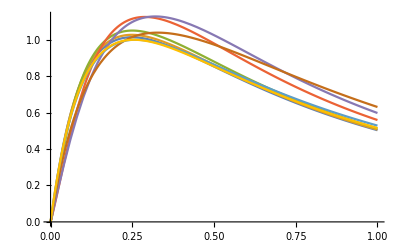

```mathematica
Plot[Evaluate[Table[ (vKS[γ] +vcorr[5, 0.01/0.02,μ,γ]/2/γ)*27/4,{μ,{0.0005,0.001,0.005,0.01,0.025,0.05,0.5,1}/0.02}]],{γ,0,1}]
```

```mathematica
(*Find local maximum*)
FindMaximum[{vks[γ] *27/4,1≤γ≤15},{γ,0.25}]
FindMaximum[{(vks[γ] +8*vcorr[5, 0.0025,μ,γ])*27/4,1≤γ≤15},{γ,0.25}]
```

{0.5,{γ→1.}}